# Reheating Era In Constrained Gauβ-Bonnet Models

## 1. Designation of scalar potential-Solution of continuity equation

We commence the study by designating the scalar potential of the model. In this case, even though two scalar functions participate in the equation of motion, only one of them is free due to the constraint in the propagation velocity of primordial tensor perturbations. This affects the continuity equation of the scalar field which now serves as either a first order differential equation for the scalar potential or as a second order differential equation for the Gauβ-Bonnet scalar coupling function. While the first is obviously the best choice since a first order differential equation can always be solved, in the present article we shall focus on the second case in order to specify the scalar potential and work with novel scalar potentials. This constraints the aforementioned scalar coupling function severely however its form is not needed in the present formalism, only its first three derivatives need to be specified.

```mathematica
V[φ_]:=Λ^4/(1+b Exp[c κ φ]);
φdot[φ_]:=H[φ]ξ'[φ]/ξ''[φ];
H20[φ_]=κ^2 V[φ]/3;
ξdot[φ_]:=ξ'[φ]φdot[φ];
difeq1=D[V[φ],φ]+3H20[φ]D[ξ0[φ],φ]/D[ξ0[φ],{φ,2}];
s=DSolve[difeq1==0,ξ0[φ],φ]
```

{{ξ0[φ]→C[2]+∫_1^φ ⅇ^((κ (-ⅇ^(-c κ K[1])/(c κ)+b K[1]))/(b c)) C[1]ⅆK[1]}}

```mathematica
ξ[φ_]:=λ∫_1^φ ⅇ^((κ (-ⅇ^(-c κ K[1])/(c κ)+b K[1]))/(b c)) ⅆK[1]
```

```mathematica
H2[φ_]:=κ^2 V[φ]/3
H[φ_]:=Sqrt[H2[φ]]
Hdot[φ_]:=-κ^2 φdot[φ]^2/2
```

## 2. Auxiliary Functions

In the second section we define a set of auxiliary parameters that are used in order to extract information about the numerical values of the observed indices.

```mathematica
Qa[φ_]:=-8ξdot[φ]H2[φ]
Qt[φ_]:=1/κ^2-8ξdot[φ]H[φ]
Qe[φ_]:=-32ξdot[φ]Hdot[φ]
E0[φ_]:=1/κ^2(1+3 Qa[φ]^2/(2Qt[φ] φdot[φ]^2))
E0dot[φ_]:=D[E0[φ],φ]φdot[φ]
Qtdot[φ_]:=D[Qt[φ],φ]φdot[φ]
```

## 3. Slow-roll Indices

In this section the slow-roll indices of the theory are designated. While we focus on 5 indices, only 4 participate in the observables and furthermore, only three have a manageable form. The first index shall be used in order to quantify the duration of inflation by making use of the e-folding number.

```mathematica
ε1[φ_]:=1/2(κ ξ'[φ]/ξ''[φ])^2
ε2[φ_]:=1-ε1[φ]-ξ'[φ]ξ'''[φ]/ξ''[φ]^2
ε3[φ_]:=E0dot[φ]/(2H[φ]E0[φ])
ε4[φ_]:=Qtdot[φ]/(2*H[φ]*Qt[φ])
```

## 4. Observed Indices

Here, the scalar spectral index of primordial curvature perturbations, the propagation velocity of scalar perturbations, the tensor-to-scalar ratio and finally the tensor spectral index are specified. In principle string corrections may be begligible.

```mathematica
nS[φ_]:=1-2(2ε1[φ]+ε2[φ]+ε3[φ])
CA[φ_]:=Sqrt[1+(Qa[φ]Qe[φ])/(2φdot[φ]^2Qt[φ]+3Qa[φ]^2)]
r[φ_]:=16Abs[( ε1[φ]-κ^2Qe[φ]/(4H[φ])) CA[φ]^3/(κ^2Qt[φ])]
nT[φ_]:=-2(ε1[φ]+ε4[φ])
(*In case the code is slow, get rid of ε3 in the scalar spectral index, ε4 in the tensor spectral index
and Qe,Qt,CA in the tensor to scalar ratio since they are infinitesimal.
nS0[φ_]:=1-2(2ε1[φ]+ε2[φ])
nT0[φ_]:=-2ε1[φ]
r0[φ_]:=16 ε1[φ]
and check afterwards if this was the correct approach at least for the inflationary era. This implies that string corrections are negligible at least during the first horizon crossing.*)
```

## 5. Initial and Final Value of the scalar field

In the present section the final value of the scalar field that signifies the end of the inflationary era is extracted. Such value is used in order to extract the initial value of the scalar field during the first horizon crossing. Such result will depend on certain model parameters and the e-folding number.

```mathematica
U1=Solve[ε1[φ]==1,φ]/.{C[1]->0};
φf=φ/.U1[[2]];
U2a=Integrate[ξ''[φ]/ξ'[φ],φ]/.φ->φl;
U2b=Integrate[ξ''[φ]/ξ'[φ],φ]/.φ->φk;
U3=Solve[N0==U2a-U2b,φk]/.{C[1]->0};
φi=φk/.U3[[1]]/.{φl->φf};
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

## 6. Numerical Results

Here we specify the free parameters of the model at hand and compute the observed indices.

```mathematica
κ=1.;N0=60.;Λ=0.091;c=1.5;λ=1.;b=1.;
φi//N
φf//N
Evaluate[nS[φ]/.φ->φi]//N
r1=r[φ]/.φ->φi//N
nT[φ]/.φ->φi//N
CA[φ]/.φ->φi//N
CA[φ]/.φ->φf//N
```

-3.23161

1.86831

0.965093

0.00109162

-0.000136452

1.

1.

## 7. Contour Plots-Dependence Of Observables

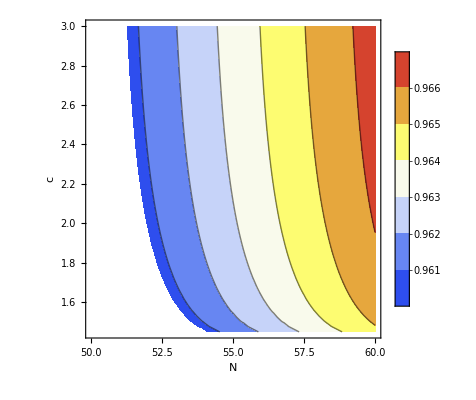

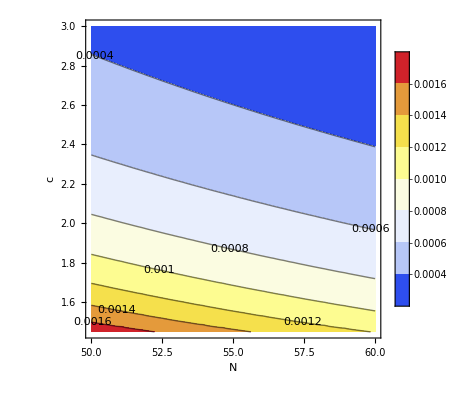

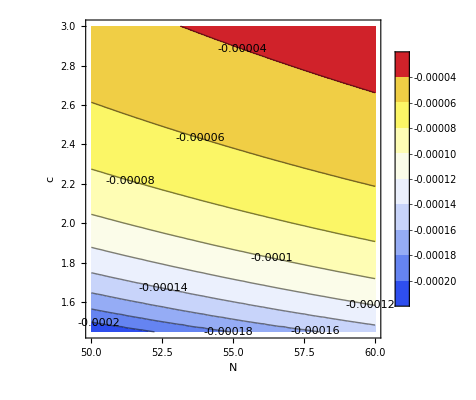

```mathematica
Clear[N0]; Clear[c];
ContourPlot[Evaluate[nS[φ]/.φ->φi],{N0,50,60},{c,1.45,3},FrameLabel->{"N","c"},PlotLegends->True,ColorFunction->"TemperatureMap",PlotRange->{0.9649-0.0042,0.9649+0.0042}]
ContourPlot[Evaluate[r[φ]/.φ->φi],{N0,50,60},{c,1.45,3},FrameLabel->{"N","c"},PlotLegends->True,ColorFunction->"TemperatureMap",ContourLabels->True]
ContourPlot[Evaluate[nT[φ]/.φ->φi],{N0,50,60},{c,1.45,3},FrameLabel->{"N","c"},PlotLegends->True,ColorFunction->"TemperatureMap",ContourLabels->True]
c=1.5;N0=60;
```

## 8. Approximations-String Corrections

For the sake of consistency, the validity of the slow-roll assumption is ascertained.

```mathematica
Hdot[φ]/.φ->φi//N
H2[φ]/.φ->φi//N
1/2 φdot[φ]^2/.φ->φi//N
V[φ]/.φ->φi//N
D[φdot[φ],φ]φdot[φ]/.φ->φi//N
3*H[φ]*φdot[φ]/.φ->φi//N
```

-1.54739×10^-9

0.0000226803

1.54739×10^-9

0.0000680409

4.58793×10^-9

7.94804×10^-7

```mathematica
24D[ξ[φ],φ] H2[φ]^2/.φ->φi//N
D[V[φ],φ]/.φ->φi//N
16*ξdot[φ]H[φ]Hdot[φ]/.φ->φi//N
24*ξdot[φ]*H[φ]*H2[φ]/.φ->φi//N
```

3.65648×10^-34

-7.94804×10^-7

-1.94273×10^-40

4.27123×10^-36

```mathematica
ε1[φ]/.φ->φi//N
ε2[φ]/.φ->φi//N
ε3[φ]/.φ->φi//N
ε4[φ]/.φ->φi//N
```

0.0000682259

0.0173172

4.3313×10^-59

-3.19286×10^-32

## 9. Algebraic Form Of X[φ]

Before we compute the corresponding reheating temperature in the end of the reheating era and extract the expression for the duration of such era, we numerically evaluate parameter X that depends on the Gauβ-Bonnet scalar coupling function and is the main object that differs between string inspired gravity with the canonical scalar field.

```mathematica
Clear[Λ];
U=Solve[x==a/Sqrt[(1-x)],x];
X0=x/.U[[1]];
X0=X0/κ^2;
a0=(4Sqrt[2]κ^3V[φ]D[ξ[φ],φ])/.φ->φf;
X=X0/.{a->a0} (*Change signs manually since mathematica is unable to compute the real solution of (-1)^(1/3).*)
```

0.333333 (1+2^(1/3)/((2-32.3307 Λ^8+3 √3 √(-4.78973 Λ^8+38.7138 Λ^16))^(1/3))+((2-32.3307 Λ^8+3 √3 √(-4.78973 Λ^8+38.7138 Λ^16))^(1/3))/2^(1/3))

## 10. Reheating Era

It is a small complex value so we do not focus on it. The reason is that 1/(1+x)+1+x=2 for small x, even complex! It is essentially a fake imaginary part.

-0.0000750369

13892.9

15.8783

9.31815×10^-13

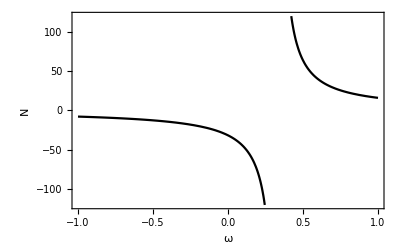

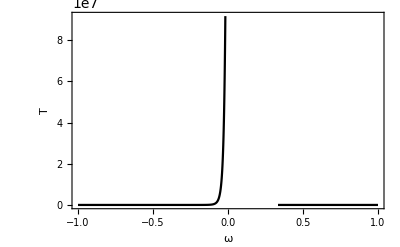

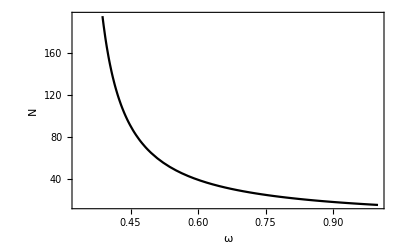

General::munfl: Exp[-777266.] is too small to represent as a normalized machine number; precision may be lost.

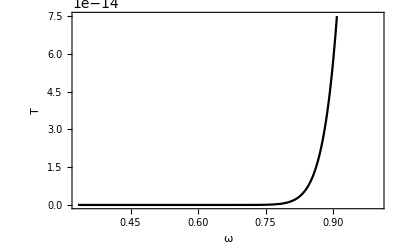

```mathematica
Λ=0.091;
X1=0.3333333333333333 (1-2^(1/3)/((-2+32.330669775565376 Λ^8-3 √3 √(-4.789728855639315 Λ^8+38.71378548654283 Λ^16))^(1/3))-((-2+32.330669775565376 Λ^8-3 √3 √(-4.789728855639315 Λ^8+38.71378548654283 Λ^16))^(1/3))/2^(1/3))//Chop
As=1.90461 10^(-9);
Hk=Pi/κ Sqrt[As r1/2];
g=100;
Vf=V[φ]/.φ->φf;
numerator=(Vf/(1-X1))^(1/4);
entry=numerator/Hk
Nre[ω_]:=4/(1-3ω)(61.6-N0-Log[entry]) 
Tre[ω_]:=(45Vf/(Pi^2g(1-κ^2X1)))^(1/4) Exp[-3(1+ω)Nre[ω]/4]
Nre[ω]/.ω->1//N
Tre[ω]/.ω->1//N
Plot[Evaluate[Nre[ω]],{ω,-1,1},FrameLabel->{"ω","N"},Frame->True]
Plot[Evaluate[Tre[ω]],{ω,-1,1},FrameLabel->{"ω","T"},Frame->True]
Plot[Evaluate[Nre[ω]],{ω,1/3,1},FrameLabel->{"ω","N"},Frame->True]
Plot[Evaluate[Tre[ω]],{ω,1/3,1},FrameLabel->{"ω","T"},Frame->True]
```

Here, Mp=1 therefore temperature is dimensionless. If we rescale the energy, given that [T]=ev, one needs to multiply temperature with 1.2 10^(19) GeV so we see already that high values for the eos can actually give us T=O(10^6) GeV. Usually 1 ev=11.606 K so we are talking about a temperature of Tre=O(10^(18)) Kelvin. Recall that Planck temperature is of order Tpl=O(10^(32)) so inflation decreases such value by a factor of 16.  From a mathematical perspective the complex values should not even bother us since this is like 1+x+1/(1+x) with x a small complex value so it does not bother us. It becomes apparent since the plot can be made as well. We could use higher Λ and make it disappear. Around Λ=0.78 the complex part vanishes. In such scale, the values are again viable but larger.

So far, the special case of ω=1/3 describing relativistic matter is not considered. It is not described by the plots above since ω=1/3 serves as a separatrix here.

This is the maximally allowed EoS according to causality, it is in the kinetic regime and not the potential regime as is the case with dark energy or in general de Sitter expansion. It essentially describes stiff matter (P=ρ) that corresponds to an energy density scaling as ρ\sim a(t)^(-6) and a(t)\sim t^(1/3), twice as fast as ordinary dust for the density and -1/3 in the scale factor! This is really interesting and perhaps could be connected to baryogenesis since the radiation dominated era is incapable of describing gravitational baryogenesis (recall that \dot R=0 at such era). It would be interesting to see how the constrained Gauβ-Bonnet model describes baryogenesis as well.

## 11. Baryogenesis.

According to Sakharov’s conditions, apart from deviation from thermal equilibrium and violation of the baryonic number induced by certain interactions, one requires a CP violating term. This could be provided by a CP violating term of gravitational origin as \partial_\mu R J^\mu (J^\mu being the baryonic current and this essentially serves as a boundary term) and for an FRW metric, only \dot R is needed. We should require a mass scale which serves as a cut-off scale and participates in the aforementioned CP violating term, this could be one of the degrees of freedom that could be used along with the previous (however hereafter fixed) parameters. The other parameter could still be the EoS to see how values close to stiff matter cosmology alter the overall phenomenology (close in order to have a successful reheating era). To proceed, we need information about the baryon-entropy ratio which shows the expected asymmetry between matter and antimatter (here we do not consider the dark sector). We require information about the temperature in which baryogenesis takes place. We could say that is somewhere between the reheating temperature and the temperature at the end of the inflationary era for consistency.  Usually one needs information about the degrees of freedom so we can use gb\sim O(1) for baryons and g\sim O(100) as before for the rest. Upper bound of the baryon asymmetry should be around 9*10^(-11).

In this procedure we need to specify the energy density), or Hubble during the time instance that corresponds to the aforementioned temperature and not the end of reheating. By assuming that the perfect fluid is in thermal equilibrium then by making use of the Stefan-Boltzmann law, the ratio between the density at the time instance baryogenesis takes place and the density at the end of the inflationary era is simply given by the ratio of the respective temperatures.

8.64525×10^-11

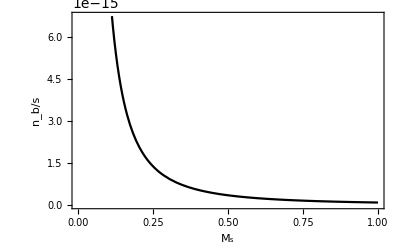

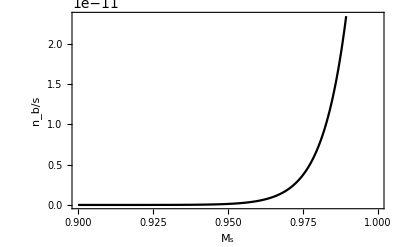

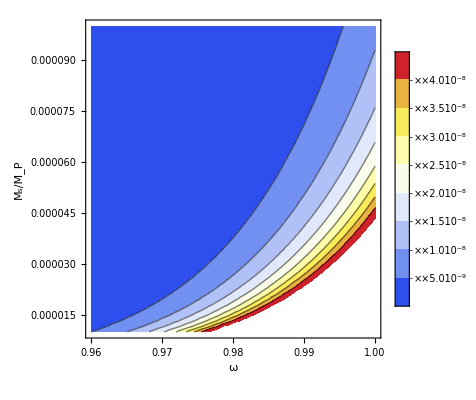

```mathematica
TD[ω_]:=  8. 10^5Tre[ω]; (* In the end we focus on ω=1. Keep in mind that TD belongs in the area [Tre,Tf]).*)
ρph[ω_]:=Pi^2/30 g Tre[ω]^4;
Tf=10^(-4); (*temperature after inflation ends in natural units, shoud be around 10^28 Kelvin, 4 orders below the Planck temperature.*)
ρf=3/2*Vf/(1-κ^2X1);
ρ[ω_]:=ρf*(TD[ω]/Tf)^(4); 
Rdot[ω_]:=κ^3Sqrt[3](1-3ω)(1+ω)ρ[ω]^(3/2)
gb=1;
asymm[ω_,Ms_]:=-15gb/(4Pi^2g)Rdot[ω]/(Ms^2TD[ω])
asymm[ω,Ms]/.{ω->1,Ms->10^(-3)}//N 
Plot[Evaluate[asymm[ω,Ms]/.ω->1],{Ms,10^(-5),1},Frame->True,FrameLabel->{"M_s","n_b/s"}]
Plot[Evaluate[asymm[ω,Ms]/.Ms->0.001],{ω,0.9,1},Frame->True,FrameLabel->{"M_s","n_b/s"}]
ContourPlot[Evaluate[asymm[ω,Ms]],{ω,0.96,1},{Ms,10^(-5),10^(-4)},FrameLabel->{"ω","M_s/M_P"},PlotLegends->True,ColorFunction->"TemperatureMap"]
```

For T=10^5 Tre and lesser values , we state that baryogenesis commences before we transition to the radiation dominated era, so we seem to be in agreement with theoretical expectations..

This is also really interesting since a small value of the reheating eos and a large value for the mass scale result in a viable baryogenesis due to gravitational effects. A viable reheating era constraints the eos to be that of stiff matter (kinetic regime) leaving us with a large mass scale.

It seems that for a mass scale close to or directly below the Planck scale, one can achieve for the model at hand a viable baryogenesis, in agreement with literature since most papers suggest that the scale of breaking of the effective theory is near the Planck scale (not a strict result since certain f(R) theories work for a mass scale 5 orders below the Planck scale). Note that the Gauss-Bonnet term here does not “participate” but it effectively appears in the energy density for which we replaced by taking advantage of its scaling with respect to temperature, and also “dictates” the fine tuning in the parameters.. This approach just goes against the usual procedure which suggests that baryogenesis commences near the radiation dominated era for en effective eos 0<ω<1/3 but it stands on its own

It may seem ad hoc however the lepton asymmetry factor should be around that value as well if we assume leptogenesis due to gravitational effects. The reason is the charge neutrality of the universe since baryons are positive, leptons negative (excluding neutrinos in this argument). In the literature there exist several articles regarding gravitational leptogenesis from string inspired theories which are parity odd, namely the Chern-Simons case. In this notebook we discuss only gravitational baryogenesis in the presence of Gauβ-Bonnet string corrections but is induced by an odd Ricci term. In the following we discuss the impact of the Gauβ-Bonnet invariant as means of explaining gravitational baryogenesis.

## 12. Gauss-Bonnet Baryogenesis.

Essentially, higher order curvature invariants used in order to describe gravitational baryogenesis suggest that the baryon asymmetry is suppressed many orders compared to the previous case. Such approach can be used if one wants to effectively decrease the mass scale of the underlying effective theory.

8.37541×10^-18

1.034×10^-11

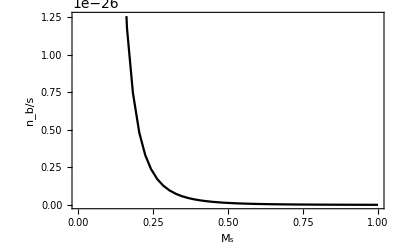

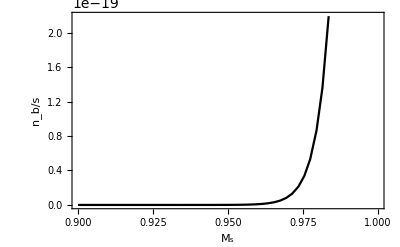

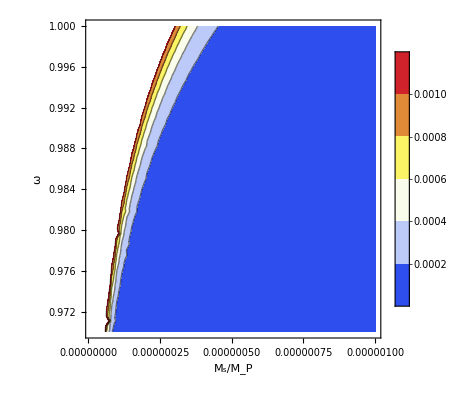

```mathematica
HD2[ω_]:=κ^2ρ[ω]/3;
GBasymm[ω_,Ms_]:=16HD2[ω]/(Ms^2)*asymm[ω,Ms] (*Can be used if one relaxes the mass scale*)
GBasymm[ω,Ms]/.{ω->1,Ms->0.001}//N
GBasymm[ω,Ms]/.{ω->1,Ms-> 3 10^(-5)}//N
Plot[Evaluate[GBasymm[ω,Ms]/.ω->1],{Ms,10^(-5),1},Frame->True,FrameLabel->{"M_s","n_b/s"}]
Plot[Evaluate[GBasymm[ω,Ms]/.Ms->0.001],{ω,0.9,1},Frame->True,FrameLabel->{"M_s","n_b/s"}]
ContourPlot[Evaluate[GBasymm[ω,Ms]],{Ms,10^(-8),10^(-6)},{ω,0.97,1},FrameLabel->{"M_s/M_P","ω"},PlotLegends->True,ColorFunction->"TemperatureMap"]
```

For the same parameters the contribution of the Gauβ-Bonnet CP violation is essentially negligible.